## 伝播の収束のチェック

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../mathematica_utilities/mathematica_plot_options.nb"}]]
(*start=18.15;
end=30;*)
start=0;
end=30;
```

Available:plot2Doption
plot3Doption
framelabel[xlabel_String,ylabel_String,size_:20]
axeslabel2D[xlabel_String,ylabel_String,size_:20]
axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20]
axeslabel[labels_List,size_: 20]
importData
jsonInfo
interpolateAndFourier
interpolateAndFourierTr
MyFourier[list_,n_]
MyInverseFourier[list_,n_]
MyDiscreteConvolve[f_,g_]
MyDiscreteConvolveUsingCn[FourierGF_]
Rv[q_]
Rs[q_]
W2dQdt[q_,w_]
getOmegaFromKandDepth
getTFromLandDepth

```mathematica
importData[filename_String,var_,n_: 0,replacement_: Missing[]]:=Module[{imported=Import[filename],processed},processed=imported/.{"NaN"|"Nan"|"null"|"nan"|Null->replacement};
If[n>0,(var/.processed)[[;;,n]],var/.processed]];

fileDir="/Volumes/home/BEM/benchmark202405";
(*fileDir="/Users/tomoaki/BEM";*)
```

5.

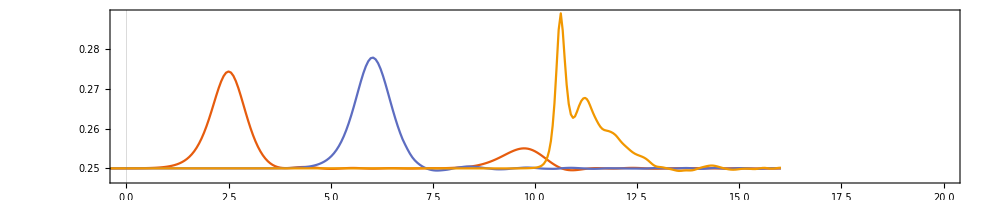

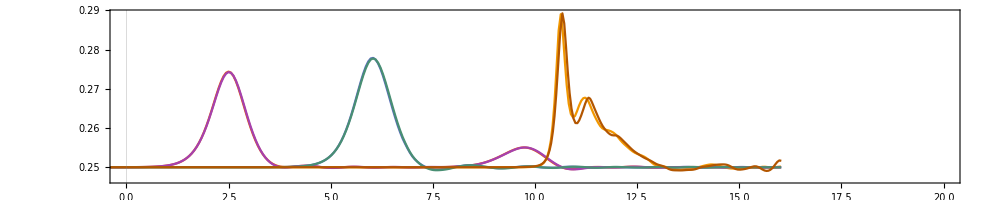

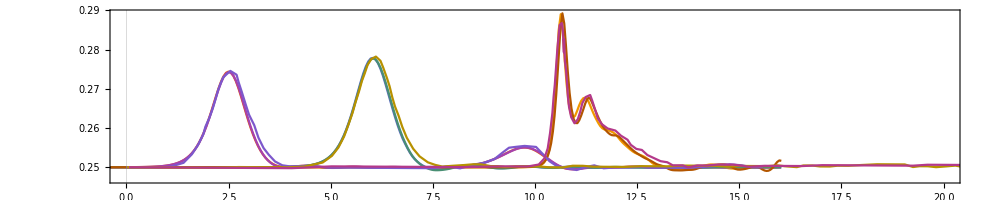

```mathematica
GoringExp1={#1,#2/100+0.25}&@@@Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge1.csv"}]];
GoringExp2={#1,#2/100+0.25}&@@@Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge2.csv"}]];
GoringExp3={#1,#2/100+0.25}&@@@Import[FileNameJoin[{NotebookDirectory[],"Goring1979Gauge3.csv"}]];
flin="/Volumes/home/BEM/benchmark202411/Goring1979_MESHwater160_DT0d06_ELEMlinear_ALElinear_ALEPERIOD1/result.json";
(*fquad="/Volumes/home/BEM/benchmark202411/Goring1979_DT0d06_ELEMlinear_ALEpseudo_quad_ALEPERIOD1/result.json";*)
fquad="/Volumes/home/BEM/benchmark202411/Goring1979_MESHwater160_DT0d06_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json";
(*shift=3.95+1*)
shift=4.+1
data={};

data=Join[data,{
Transpose[{importData[flin,"simulation_time"]-shift,importData[flin,"gauge0_intersection",3]}],
Transpose[{importData[flin,"simulation_time"]-shift,importData[flin,"gauge1_intersection",3]}],
Transpose[{importData[flin,"simulation_time"]-shift,importData[flin,"gauge2_intersection",3]}]}];

ListPlot[data,PlotRange->{{0,20},All},Joined->True,AspectRatio->1/5,ImageSize->1000,Evaluate[plot2Doption]]


data=Join[data,
{Transpose[{importData[fquad,"simulation_time"]-shift,importData[fquad,"gauge0_intersection",3]}],
Transpose[{importData[fquad,"simulation_time"]-shift,importData[fquad,"gauge1_intersection",3]}],
Transpose[{importData[fquad,"simulation_time"]-shift,importData[fquad,"gauge2_intersection",3]}]
}];

ListPlot[data,PlotRange->{{0,20},All},Joined->True,AspectRatio->1/5,ImageSize->1000,Evaluate[plot2Doption]]

AppendTo[data,GoringExp1];
AppendTo[data,GoringExp2];
AppendTo[data,GoringExp3];
ListPlot[data,PlotRange->{{0,20},All},Joined->True,AspectRatio->1/5,ImageSize->1000,Evaluate[plot2Doption]]
```

```mathematica
jsons={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALEpseudo_quad",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALElinear","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMpseudo_quad_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d025_ELEMlinear_ALElinear",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALElinear","Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad"};
jsons=FileNameJoin[{fileDir,#,"result.json"}]&/@jsons;
```

```mathematica
ExtractInfoFromPath[path_String]:=Module[{splitPath,mesh,h,dt,elementBVPandIVP,elementALE,ALEperiod},splitPath=StringSplit[path,{"_","/"}];
(*Hの値を抽出*)
h=SelectFirst[splitPath,StringContainsQ[#,"H0d"]&];
h=StringReplace[h,{"H0d"->"H=0."}];

(*dtの値を抽出*)
dt=SelectFirst[splitPath,StringContainsQ[#,"DT0d"]&];
dt=StringReplace[dt,{"DT0d"->"dt=0."}];

(*meshの値を抽出*)
mesh=SelectFirst[splitPath,StringContainsQ[#,"float0d"]&];
mesh=StringReplace[mesh,{"float0d"->"dl=0."}];

(*BVPとIVPのための要素を抽出*)
elementBVPandIVP=SelectFirst[splitPath,StringContainsQ[#,"ELEM"]&];
elementBVPandIVP=StringReplace[elementBVPandIVP,"ELEM"->"BVP:"];

(*ALEの要素を抽出*)
elementALE=SelectFirst[splitPath,StringContainsQ[#,"ALE"]&];
elementALE=StringReplace[elementALE,"ALE"->"ALE:"];

(*ALE periodの値を抽出*)
ALEperiod=SelectFirst[splitPath,StringContainsQ[#,"ALEPERIOD"]&,"ALEPERIOD1"];
ALEperiod=StringReplace[ALEperiod,{"ALEPERIOD"->"ALE Step Period:"}];


(*結果を返す*)
{mesh,h,dt,elementBVPandIVP,elementALE,ALEperiod}];

(*gauges={"gauge2_intersection","gauge22_intersection"};*)
(*gauges={"gauge4_intersection","gauge23_intersection"};*)
gauges={"gauge2_intersection","gauge22_intersection"};
colors={Blue,Red,Darker[Green],Black};
(*---------------------------------------------*)
compare[jsons_,zrange_:(5+{-0.06,0.06}),surface_:5]:=Module[{size,ratio,h,legend},
size=700;
ratio=1/5;
h=surface;

select[json_,name_]:=Module[{data},
Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&]
];

selectAndNegateMean[json_,name_]:=Module[{data},
data=Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&];
mean=Mean[Transpose[data][[2]]];
{#1,#2-mean}&@@@data
];
(*colors={Blue,Orange,Green,Magenta};*)

(*colors={RGBColor[0.4,0.7,0.9],(*Sky Blue*)RGBColor[0.9,0.6,0.0],(*Soft Orange*)RGBColor[0.5,0.3,0.7],(*Plum Purple*)RGBColor[0.3,0.7,0.0]  (*Apple Green*)};*)



legend=LineLegend[colors[[;;Length[jsons]]],StringJoin [Riffle[ExtractInfoFromPath[#],", "]]&/@jsons,
LegendMarkerSize->{{40,5}},
LabelStyle->{FontFamily->"Times",FontSize->15},
LegendLayout->"Row",
LegendFunction->"Frame"];
(*=======================================================================*)
Grid[
{{legend,SpanFromLeft},
{
Labeled[Column[Table[ListPlot[
Table[select[json,name],{json,jsons}]
,PlotRange->{All,h+zrange}
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio
,ImageSize->size
(*,Epilog->{{Dashed,Line[{{start,h+0.05},{end,h+0.05}}]},{Dashed,Line[{{start,h-0.05},{end,h-0.05}}]}}*)
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.925,0.15}]]
,Joined->True
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]],
{name,gauges}]]
,framelabel["Time [s]","Surface Elevation [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
},
{
Labeled[
Row[Table[ListStepPlot[Table[{#1,#2}&@@@(interpolateAndFourier[#1,#2]&@@Transpose[selectAndNegateMean[json,name]]),{json,jsons}]
,Center
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio*2.
,ImageSize->size/2.
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.85,0.85}]]
,PlotRange->{{0.,3},{All,zrange[[2]]}(*,{0,0.026}*)}
,Joined->False
,Filling->Bottom
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]
],
{name,gauges}]]
,framelabel["Frequency [s^-1]","Amplitude.08 [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
}
}
]
]
(*=======================================================================*)
compareSimple[jsons_,zrange_:(5+{-0.06,0.06}),surface_:5]:=Module[{size,ratio,h,legend},
size=700;
ratio=1/5;
h=surface;

select[json_,name_]:=Module[{data},
Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&]
];

selectAndNegateMean[json_,name_]:=Module[{data},
data=Select[Transpose[{importData[json,"simulation_time"],importData[json,name,3]}],start≤#[[1]]≤end&];
mean=Mean[Transpose[data][[2]]];
{#1,#2-mean}&@@@data
];
(*colors={Blue,Orange,Green,Magenta};*)

(*colors={RGBColor[0.4,0.7,0.9],(*Sky Blue*)RGBColor[0.9,0.6,0.0],(*Soft Orange*)RGBColor[0.5,0.3,0.7],(*Plum Purple*)RGBColor[0.3,0.7,0.0]  (*Apple Green*)};*)

legend=LineLegend[colors[[;;Length[jsons]]],StringJoin [Riffle[ExtractInfoFromPath[#],", "]]&/@jsons,
LegendMarkerSize->{{40,5}},
LabelStyle->{FontFamily->"Times",FontSize->15},
LegendLayout->"Row",
LegendFunction->"Frame"];

Grid[
{{legend,SpanFromLeft},
{
Labeled[Column[Table[ListPlot[
Table[select[json,name],{json,jsons}]
,PlotRange->{All,h+zrange}
,PlotStyle->colors
,GridLines->Automatic
,AspectRatio->ratio/1.5
,ImageSize->size
(*,Epilog->{{Dashed,Line[{{start,h+0.05},{end,h+0.05}}]},{Dashed,Line[{{start,h-0.05},{end,h-0.05}}]}}*)
,Epilog->Inset[Framed[Style["d="<>ToString@importData[jsons[[1]],name,1][[1]]<>" m",10],Background->LightYellow],Scaled[{0.05,0.15}]]
,Joined->True
,BaseStyle->Directive[FontFamily->"Times New Roman",FontSize->16]
,Evaluate[plot2Doption]],
{name,{
"gauge2_intersection",
"gauge7_intersection",
"gauge12_intersection",
"gauge17_intersection",
"gauge22_intersection"}}]]
,framelabel["Time [s]","Surface Elevation [m]",16,{0,Pi/2}],{Bottom,Left}
,ImageMargins->{{10,0},{0,0}}
]
}
}
,Spacings->0]
]
(*=======================================================================*)
fileName[{H_,L_,WAVE_,MESH_,DT_,ELEM_,ALE_}]:=Module[{formatNumber},
formatNumber[n_]:=StringReplace[ToString[N[n]],"."->"d"];
StringJoin["Tanizawa1996_",
"H",formatNumber[H],
"_L",formatNumber[L],
"_WAVE",WAVE,
"_MESH",MESH,
"_DT",formatNumber[DT],
"_ELEM",ELEM,
"_ALE",ALE]]
```

```mathematica
(*gaugeのx座標*)
FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}]
importData[FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}],gauges[[2]],1][[1]]
importData[FileNameJoin[{fileDir,fileName[{0.1,1.8,"potential","water_no_float0d08",0.05,"linear","linear"}],"result.json"}],gauges[[1]],1][[1]]
```

/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear/result.json

Import::nffil: Importの最中にファイル/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge22_intersection/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

gauge22_intersection/.$Failed

Import::nffil: Importの最中にファイル/Volumes/home/BEM/benchmark202405/Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(gauge2_intersection/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

gauge2_intersection/.$Failed

```mathematica
(*少しチェック*)
F=getOmegaFromLandDepth[1.8,50.]/(2*π)
T=1/F
```

0.93134

1.07372

```mathematica
2*π/getOmegaFromLandDepth[1.8,5.]
```

1.07372

#### 減衰へのALE毎回．meshの細かさの影響（おいおい）

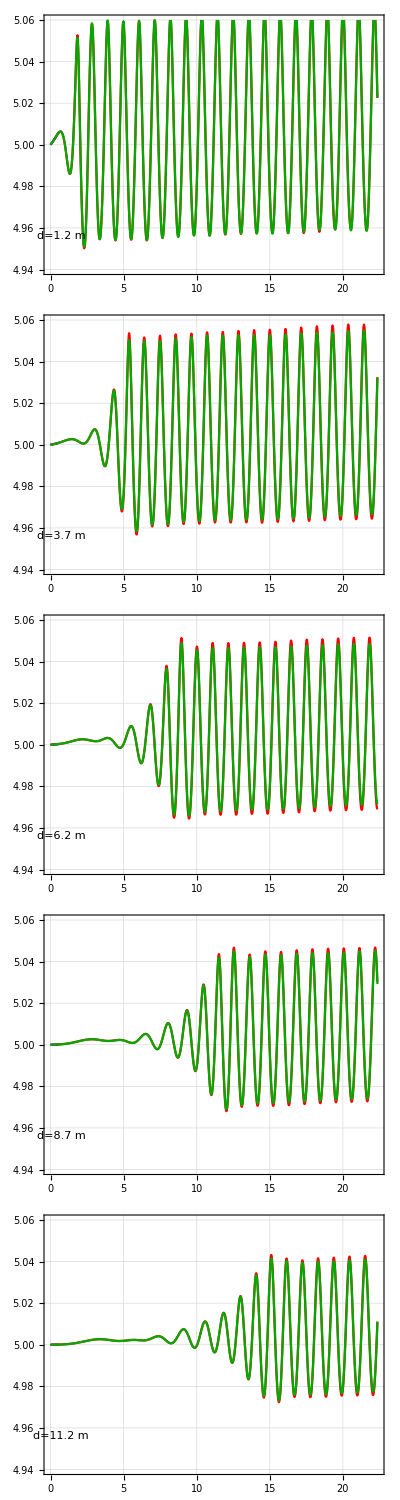
| 
-Graphics-Time [s]Surface Elevation [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d1.png

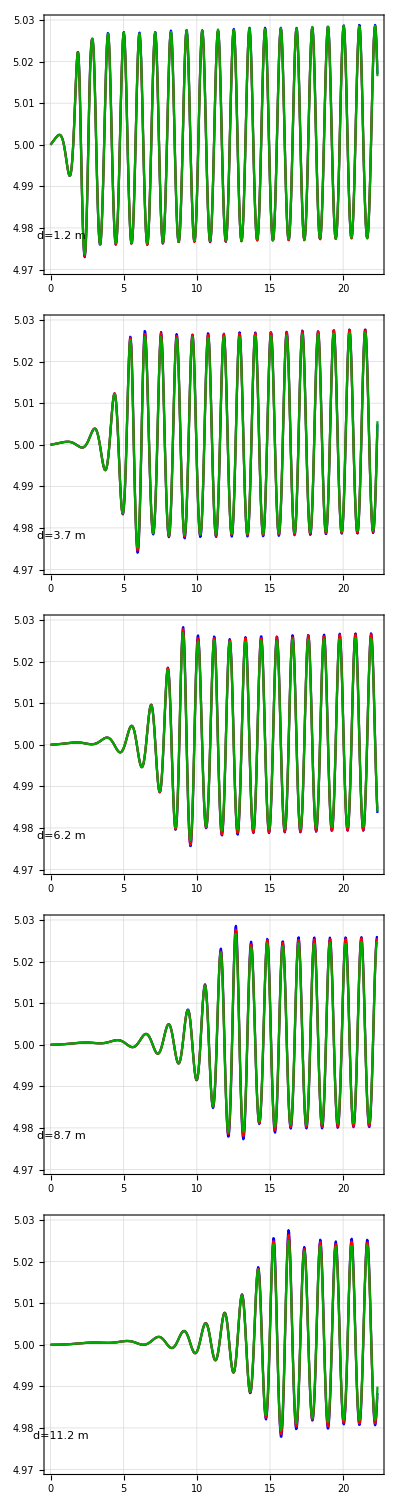
| 
-Graphics-Time [s]Surface Elevation [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d05.png

ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．

```mathematica
zrange={-0.06,0.06};
{start,end}={0.,17.+T*5};

ALE="linear";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};
*)
comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d06_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"};
fig=compareSimple[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]
Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d1.png",fig,ImageResolution->300]

comp0d08={
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d06_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d05_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"};

fig=compareSimple[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,{-0.03,0.03}]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/mesh_quality_ELEMlinear_ALElinear_H0d05.png",fig,ImageResolution->300]

Text["ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．"]
```

#### 減衰へのALE頻度の影響 ALE:linear

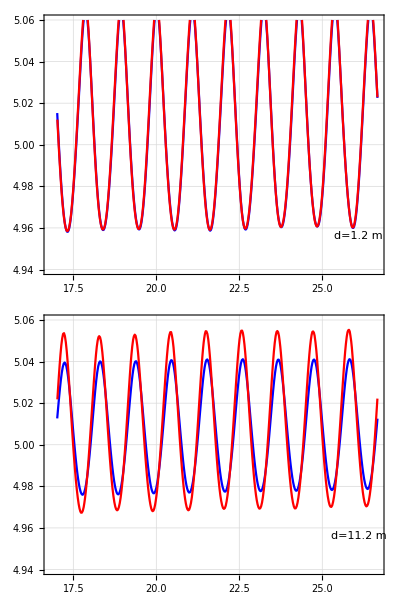
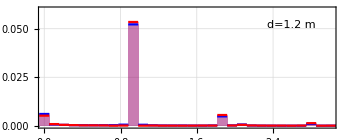
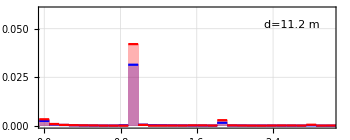
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_comparison.png

ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．

```mathematica
zrange={-0.03,0.03}*2;
{start,end}={17.,17.+T*9};

ALE="linear";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};
*)
comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};

fig=compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_comparison.png",fig,ImageResolution->225]

Text["ALEの頻度を1/3にすると，波の減衰が大幅に抑えられた．"]
```

#### 減衰へのALE頻度の影響 ALE:pseudo-quad

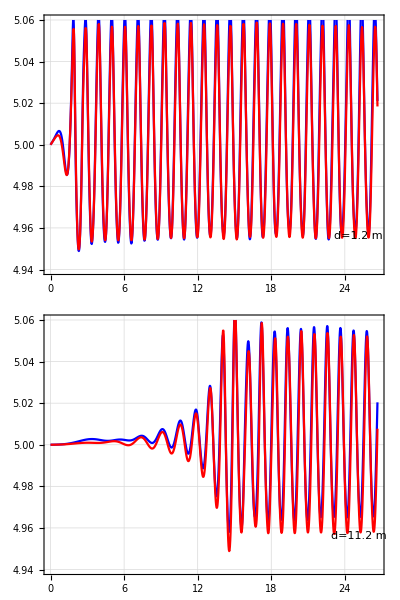
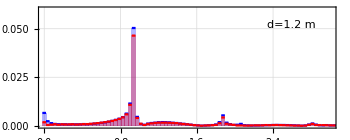
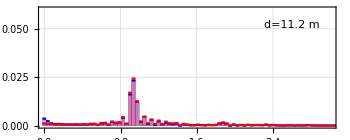
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_pseudo_comparison.png

ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．

```mathematica
zrange={-0.03,0.03}*2;
{start,end}={0.,17.+T*9};
ALE="pseudo_quad";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};*)

comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};


fig=compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_pseudo_comparison.png",fig,ImageResolution->225]

Text["ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．"]
```

#### BVPに擬2次要素を使った場合

{Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1,Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1}

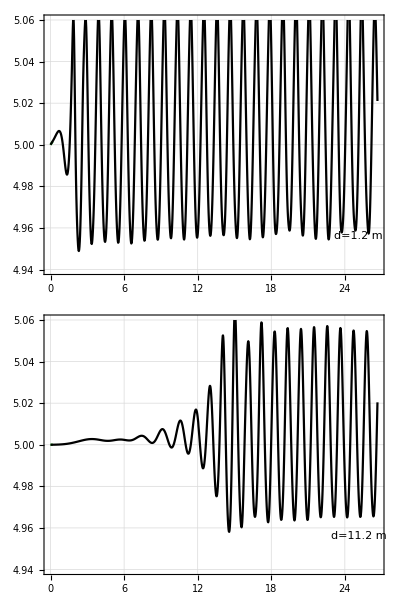
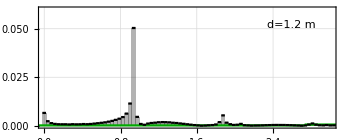
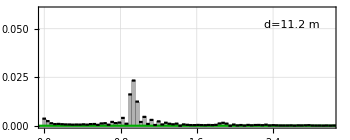
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/MESH0d08_ELEMpseudo_quad_H0d1.png

ALEを頻繁にメッシュに適用してメッシュを均一にしなければ，pseudo-quadの精度は悪化し，計算が破綻してしまうようだ．
pseudo-quadは，歪なメッシュにおいては計算が不安定になる可能性がある．

```mathematica
zrange={-0.03,0.03}*2.;
colors=RotateLeft[colors,2];
ALE="pseudo_quad";
BVP="linear";
comp={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMpseudo_quad_ALE"<>ALE<>"_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD1"}

compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp,zrange]

Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/MESH0d08_ELEMpseudo_quad_H0d1.png",%,ImageResolution->225]

Text["ALEを頻繁にメッシュに適用してメッシュを均一にしなければ，pseudo-quadの精度は悪化し，計算が破綻してしまうようだ．
pseudo-quadは，歪なメッシュにおいては計算が不安定になる可能性がある．"]
```

#### 最も良いと思われる計算

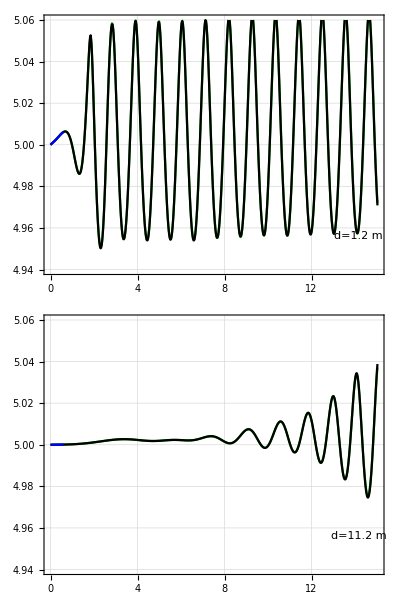
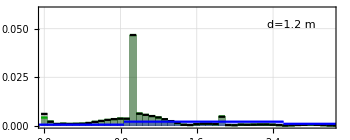
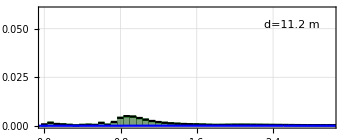
| 
-Graphics-Time [s]Surface Elevation [m] | 
-Graphics--Graphics-Frequency [s^-1]Amplitude.08 [m] |

ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．

```mathematica
zrange={-0.03,0.03}*2;
{start,end}={0.,T*14};
ALE="pseudo_quad";
fileDir="/Volumes/home/BEM/benchmark202405";
(*comp0d07={fileName[{0.1,1.8,"potential","water_no_float0d07",0.05,"linear",ALE}],
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALE"<>ALE<>"_ALEPERIOD3"};*)

comp0d08={
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d08_DT0d05_ELEMlinear_ALElinear_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d07_DT0d05_ELEMlinear_ALElinear_ALEPERIOD1",
"Tanizawa1996_H0d1_L1d8_WAVEpotential_MESHwater_no_float0d06_DT0d05_ELEMlinear_ALElinear_ALEPERIOD1"};


fig=compare[FileNameJoin[{fileDir,#,"result.json"}]&/@comp0d08,zrange]

(*Export["/Users/tomoaki/Library/CloudStorage/Dropbox/writingworkshop/2024/pseudo_quad/image/dl0d08_ALE_frequency_pseudo_comparison.png",fig,ImageResolution->225]
*)
Text["ALEがpseudoの場合でも頻度を1/3にすると，波の減衰が大幅に抑えられた．ただし，ALEがlinearの場合よりもALE pseudo quadは減衰が生じにくい．"]
```

{141.12,152.64,190.08,204.48}

no. | title | length
1 | cpu_time | 378
2 | eq_of_motion | 378
3 | gauge0_intersection | 378
4 | gauge1_intersection | 378
5 | gauge2_intersection | 378
6 | gradPhi_worst_grad | 378
7 | gradPhi_worst_iteration | 378
8 | gradPhi_worst_value | 378
9 | simulation_time | 378
10 | wall_clock_time | 378
11 | water_E | 378
12 | water_EK | 378
13 | water_EP | 378
14 | water_face_size | 378
15 | water_point_size | 378
16 | water_volume | 378

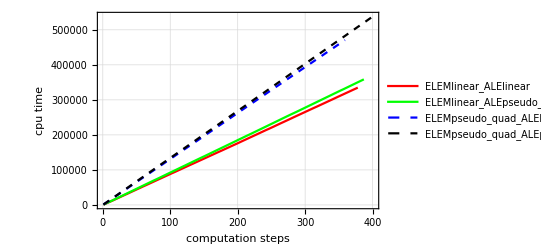

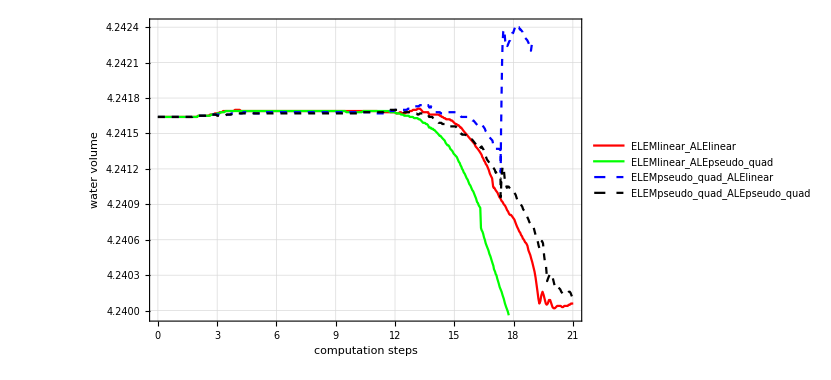

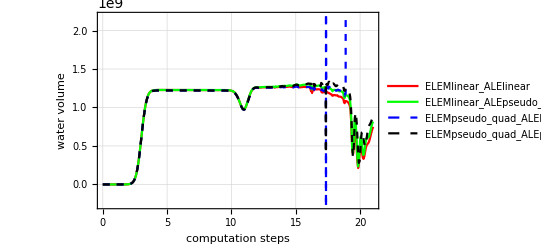

```mathematica
list={
"ELEMlinear_ALElinear",
"ELEMlinear_ALEpseudo_quad",
"ELEMpseudo_quad_ALElinear",
"ELEMpseudo_quad_ALEpseudo_quad"};
(*clist={5000,6000,7000,8000}*0.96;*)
clist={4900,5300,6600,7100}*0.96*0.03

mainname="/Volumes/home/BEM/benchmark202411/Goring1979_MESHwater160_DT0d03_";

jsonInfo[mainname<>list[[1]]<>"_ALEPERIOD1/result.json"]

Show[ListPlot[
Table[importData[mainname<>name<>"_ALEPERIOD1/result.json","cpu_time"]
(*}*)
,{name,list}]
,FrameLabel->framelabel["computation steps","cpu time"]
,PlotStyle->{Red,{Green},{Blue,Dashed},{Black,Dashed}}
,PlotLegends->list
,GridLines->Automatic
(*,PlotRange->{{0,10},Automatic}*)
,Evaluate[plot2Doption]]
(*,
Plot[Table[c*x,{c,clist}],{x,0,10}]*)
]

Show[ListPlot[
Table[
Transpose@{
importData[mainname<>name<>"_ALEPERIOD1/result.json","simulation_time"],
(data=importData[mainname<>name<>"_ALEPERIOD1/result.json","water_volume"])(*/data[[1]]*)
}
(*}*)
,{name,list}]
,FrameLabel->framelabel["computation steps","water volume"]
,PlotStyle->{Red,{Green},{Blue,Dashed},{Black,Dashed}}
(*,PlotRange->{Automatic,{0.999,1.001}}*)
,PlotLegends->list
,GridLines->Automatic
(*,PlotRange->{{0,10},Automatic}*)
,Evaluate[plot2Doption]]
(*,
Plot[Table[c*x,{c,clist}],{x,0,10}]*)
]

Show[ListPlot[
Table[
Transpose@{importData[mainname<>name<>"_ALEPERIOD1/result.json","simulation_time"],
(data=importData[mainname<>name<>"_ALEPERIOD1/result.json","water_EK"])/data[[1]]}
,{name,list}]
,FrameLabel->framelabel["computation steps","water volume"]
,PlotStyle->{Red,{Green},{Blue,Dashed},{Black,Dashed}}
,PlotLegends->list
,GridLines->Automatic
(*,PlotRange->{{0,10},Automatic}*)
,Evaluate[plot2Doption]]
(*,
Plot[Table[c*x,{c,clist}],{x,0,10}]*)
]
```